λ = 0.5

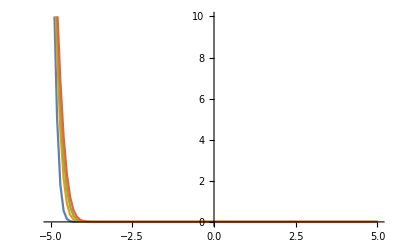

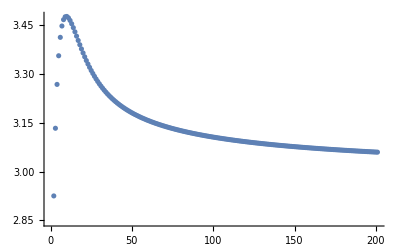

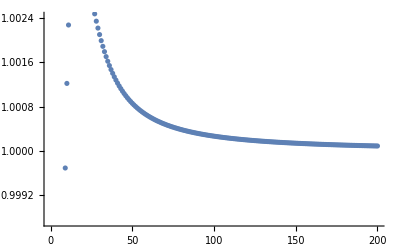

```mathematica
(*Crank-Nicolson Method*)
α=.5; (* IN ORDER TO SEE PLOT FOR λ = .35, .4, .45, .5, .55 JUST SET α = TO DESIRED λ *)
	    (* NOTICE THAT FOR λ > 1/2, THE APPROXIMATION REMAINS STABLE*)
Δx=.1;
Δt=.01;
λ = α Δt/Δx^2;
Print["λ = ", α Δt/Δx^2];
(*Vector u initialization*)
u={}; (* the u vector holds the temperature at each Subscript[x, i] during a given t*)
x = {}; (* the vector x holds the value each Subscript[x, i], used for plotting *)
For[i=-5, i≤5,i+=Δx,
(*u(Subscript[x, i],0) = 0*)
AppendTo[u,0];
AppendTo[x,i];
];
(*u(-5,0) = 20 *)
(*u(5,0) = 0 *)
u[[1]]=20;

(*Constructing the 2 Matrices*)
A = IdentityMatrix[Length[u]];
B = IdentityMatrix[Length[u]];

(* A gives n+1/2 timestep from n*)
For[i=2,i≤Length[u]-1,i++,
A[[i,i]] = 2(1-λ);
A[[i,i-1]]=λ;
A[[i,i+1]]=λ;
];
A = .5*A;
Ainv= Inverse[A];
(*This inverse of B gives n+1 timestep from the n+1/2*)
For[i=2,i≤Length[u]-1,i++,
B[[i,i]] = 2(1+λ);
B[[i,i-1]]=-λ;
B[[i,i+1]]=-λ;
];
B = .5*B;

(*Constructing the discrete fourier transform matrix*)
M = Length[u];
dftm = {};
(* from 0 to 7 *)
For[k =0, k ≤ M -1, ++k, 
(* make a new basis vector for each frequency *)
row = {};
For[i =0, i ≤ M-1, ++i,
 (* for a given frequency k, at each ith location compute the component of that basis vector *)
xi = 2*Pi/M * i;
AppendTo[row, E^(I*k*xi)];
];
AppendTo[dftm,row];
];
dftm = dftm/Sqrt[M];

(*Now begin iteration, i.e. timestepping*)
ulist = {};
clist = {};

For[t=0.0,t≤2,t+=Δt,
If[(t==.03||t==.06||t==.08||t==.1),
AppendTo[ulist,u];
];
u=A.u;(*Subscript[u, t+1/2] = A*u *)
u=LinearSolve[B,u];(*Subscript[u, t+1] = B^-1*Subscript[u, t+1/2], so we use Linear Solve*)
						(* We could also compute B^-1 and multiply it by u*)
c = N[Simplify[dftm.u]];
AppendTo[clist,Abs[c[[12]]]]; (*choose an arbitrary coefficient*)
];

ratiolist = {};
For[i=1,i≤Length[clist]-1, i++,
AppendTo[ratiolist,Abs[clist[[i]]]/Abs[clist[[i+1]]]];
];


ListLinePlot[{Transpose[{x,ulist[[1]]}], Transpose[{x,ulist[[2]]}], Transpose[{x,ulist[[3]]}], Transpose[{x,ulist[[4]]}]}, PlotRange->{0,10}]
ListPlot[clist] (* Plot moduli of the 12th coefficient in each fourier interpolation at each timestep*)
ListPlot[ratiolist](* Plot ratio of the moduli *)
```